## Getting Started:

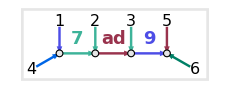
Constructing
Concrete Colour Tensors
-Graphics-
for Simple Gauge Theories
Jacob L. Bourjaily, Michael Plesser,
and Philip Velie, 2026

```mathematica
SetDirectory[NotebookDirectory[]];
<<colour_tensors.m
```

### Installing the Package

```mathematica
installColourTensors
```

## Simple Lie Algebras and their Representations (in the Abstract)

### Naming of Simple Lie Algebras: Cartan’s Conventions

The Cartan system of naming is preferred, but support exists to convert other familiar naming of Lie algebras (such “so[10]” or “e[4]”).

```mathematica
egAlgebras={su[6],so[13],sp[14],d[8],e[4],e[5],e[6],e[7],e[8],f[4],g[2]}
nice[%]
```

Notice that nice will automatically re-label any algebras according to Cartan’s conventions.

### Weight Systems for Lie Algebras (and Conventions)

#### dynkinDiagram[algebra_]: gives a labelled Dynkin diagram for each simple Lie algebra

Simple Lie algebras are characterized by their Dynkin diagrams, which encode their weight systems/root lattices. 
These can be drawn using the function 
dynkinDiagram[algebra_]:

```mathematica
dynkinDiagram/@{a[8],b[8],c[8],d[8],e[6],e[7],e[8],f[4],g[2]}//Column
```

Although the Dynkin diagrams are themselves fairly standard, conventions for the association between nodes and the simple roots vary wildly. 

Notice: our conventions are indicated in the labeling of nodes on each Dynkin diagram.

#### showLatticeData[algebra_]: gives stylized display of information about each simple Lie algebra

The conventional choice of how simple roots of weight lattices are ordered has many knock-on-effects for how weight-systems are organized/ordered, and affects the ordering of rows/columns of the 
Cartan matrix, weight metrics, etc. 

A summary of all convention-related choices made for the weight lattices of each of the simple Lie algebras can be obtained via 
showLatticeData[algebra_]:

```mathematica
showLatticeData/@{a[8],b[8],c[8],d[8],e[6],e[7],e[8],f[4],g[2]}//Column
```

Note: the individual bits of data in these summaries can be obtained separately:

#### cartan[algebra_]: returns the Cartan matrix

```mathematica
cartan/@{a[4],b[4],c[4],d[4],e[6],e[7],e[8],f[4],g[2]}//nice
```

#### weightMetric[algebra_]: returns the weight metric

```mathematica
weightMetric/@{a[4],b[4],c[4],d[4],e[6],e[7],e[8],f[4],g[2]}//nice
```

Note: this data is computed from our each algebra’s defining representation; they are not pre-stored.

#### positiveRoots[algebra_] and positiveWeights[algebra_]:

The root-system describing a simple Lie algebra is given by positive/negative roots which are sums over positive roots with integer coefficients. 
The roots consist of these integer-valued coefficients, and the weights are the vectors themselves

```mathematica
{positiveRoots[e[6]],positiveWeights[e[6]]}//nice
```

```mathematica
{positiveRoots[f[4]],positiveWeights[f[4]]}//nice
```

Note: these two sets of data are simply related by the Cartan matrix: 
	roots.cartan=weights; or, equivalently, 
	roots=weights.inverse[cartan].

#### coxeter[algebra_] and dualCoxeter[algebra_]:

The Coxeter number is defined as 1 + the sum of the marks of the highest root. 
The dual Coxeter number is defined as 1 + the sum of the co-marks of the highest root.

```mathematica
egAlgebras={a[1],b[2],g[2],c[3],d[4],f[4],e[6],e[7],e[8]};
MatrixForm[{nice/@#, coxeter/@#, dualCoxeter/@#}&@egAlgebras]
```

### Dynkin-(‘Highest-Weight-’)Labelling of Irreducible Representations

#### Basic Syntax of Dynkin Labels

Irreducible representations of any rank-k, simple Lie algebra can be identified by their highest-weights or “Dynkin Label”. 
These are k-tuples of non-negative integers. Any choice of such a k-tuple corresponds to some irreducible representation of the Lie algebra.

In order to disambiguate between algebras of the same rank, we conventionally use the following syntax for Dynkin labels

w[algebraType_][highestWeightLabelSequence__]

```mathematica
egIrrepLabel=w[e]@@RandomInteger[{0,5},{6}]
nice[%]
```

#### adjointDynkinLabel[algebra_]: returns the Dynkin Label for the Adjoint Representation (‘θ’)

The adjoint representation’s Dynkin label (often denoted ‘θ’) can be identified by
e.g.

```mathematica
adjointDynkinLabel[e[7]]
nice[%]
```

We can summarize this for each for the types of Lie algebras as follows:

```mathematica
{nice[#],adjointDynkinLabel[#]}&/@{a[8],b[8],c[8],d[8],e[6],e[7],e[8],f[4],g[2]}//Grid
```

#### showFundamentalIrrepLabels[algebra_]:

A special role is played by irreducible representations of fundamental weight
—namely, those with a Dynkin label corresponding to a row of the (k×k) identity matrix.

As the organization of these irreducible representations effectively disambiguates the 
Dynkin-labeling of all irreducible representations, a summary of these representations’ Dynkin labels is given by

showFundamentalIrrepLabels[algebra_]:

```mathematica
showFundamentalIrrepLabels/@{a[8],b[8],c[8],d[8],e[6],e[7],e[8],f[4],g[2]}//Column
```

### Weight Systems for Irreducible Representations

#### showWeightLattice[dynkinLabel_]:

Irreducible representations are associated with a system of weights—which are arranged into a spindle starting with the highest-weight

```mathematica
showWeightLattice[w[e][1,0,0,0,0,0]]
```

Note: alternative syntax allowed
showWeightLattice[algebra_] returns that for the adjoint representation
showWeightLattice[F[algebra_]] returns that for the defining/‘fundamental’ representation

```mathematica
{showWeightLattice[d[4]],positiveWeights[d[4]]}//nice
```

```mathematica
showWeightLattice[F[f[4]]]
```

#### showRootLattice[dynkinLabel_]:

All the weights of the adjoint lattice are integer multiples of simple roots. 
These roots are related to weights as 
root=weight.cartan, or 
weight=root.(inverse[cartan])

```mathematica
{positiveWeights[a[4]],positiveRoots[a[4]],showWeightLattice[a[4]],showRootLattice[a[4]]}//nice
```

For non-adjoint irreducible representations, weights are not necessarily integer combinations of simple roots; 
their coefficients (with respect to the basis of simple roots) are called marks. 
These coefficients are returned by the function showRootLattice.

```mathematica
{showRootLattice[F[f[4]]],showWeightLattice[F[f[4]]]}
```

```mathematica
{showRootLattice[F[d[4]]],showWeightLattice[F[d[4]]]}
```

#### representationWeights[dynkinLabel_] and representationRoots[dynkinLabel_]:

In case the user wants access to the output of “showWeightLattice” or “showRootLattice” without formatting, this can be obtained from 
representationWeights[dynkinLabel_] and representationRoots[dynkinLabel_], respectively.

```mathematica
representationRoots[g[2]]
{nice[%],showRootLattice[g[2]]}
```

```mathematica
representationWeights[g[2]]
{nice[%],showWeightLattice[g[2]]}
```

### Exempli Gratia: Finding Dynkin-Labels for Irreducible Representations of Specified Dimension

It is sometimes common (especially for physicists to) “identify” or label irreducible representations by their dimension.

This is unequivocally problematic, as there are often multiple irreducible representations of identical dimension; 
but often, this information is sufficient to uniquely identify an irreducible representation.

#### irrepDimensionToDynkinLabels[algebra_][dimension_]:

```mathematica
irrepDimensionToDynkinLabels[e[8]][248]
nice[%]
```

Note: when there are multiple irreducible representations of a given dimension, irrepDimensionToDynkinLabels will return the Dynkin labels of all such irreducible representations

```mathematica
irrepDimensionToDynkinLabels[e[6]][351]
nice[%]
```

#### Exempli Gratia: Finding All Irreducible Representations within some Bounded Dimension

```mathematica
t0=AbsoluteTime[];
irrepList=Join@@(irrepDimensionToDynkinLabels[e[6]]/@Range[10^4])
niceTime[AbsoluteTime[]-t0]
nice[irrepList]
```

### Analysis of Irreducible Representations (using Weight System Data (only))

#### representationDimension[dynkinLabel_]:

```mathematica
egIrrepLabel=w[e]@@RandomInteger[{0,5},{6}]
nice[%]
representationDimension[egIrrepLabel]
```

Note: the function representationDimension can also be provided arguments consisting of the irreducible-representation decomposition of non-irreducible representations.

```mathematica
egIrrep=ad[e[6]];
egReducibleRep=tensorPowerDecomposition[egIrrep,4]
nice[%]
representationDimension[egReducibleRep]
%===Power[representationDimension[egIrrep],4]
egReducibleRep/.w[e_][label__]:>representationDimension[w[e][label]]
%/.times->Times/.plus->Plus
```

#### conjugateRep[dynkinLabel_]:

Lie algebras a[k_] (with k>1), d[k_] (for odd-k) and e[6] admit a non-trivial automorphism called “conjugation” 
which maps irreducible representations to other irreducible representations.

```mathematica
w[a]@@@IdentityMatrix[7]
Transpose[{%,conjugateRep/@%}]//Grid
```

```mathematica
w[d]@@@IdentityMatrix[7]
Transpose[{%,conjugateRep/@%}]//Grid
```

```mathematica
w[e]@@@IdentityMatrix[6]
Transpose[{%,conjugateRep/@%}]//Grid
```

#### realRepresentationQ[dynkinLabel_]:

A representation is real if it is equivalent to its image under conjugation. 
(Notice that all all representations of b[k],c[k],e[7],e[8],f[4], and g[2] are real.)

```mathematica
{nice[#],#,Style[realRepresentationQ[#],Bold]}&/@(w[e]@@@IdentityMatrix[6])//Grid
```

#### pseudoRealRepresentationQ[dynkinLabel_]:

It is sometimes valuable to differentiate among the real irreducible representations, 
those for which R⋀R⊃1 (“pseudoReal”) from those for which R⊙R⊃1 (“real-real”). 
For our purposes, we consider the later case to be those representations which are real but not psuedoReal.

```mathematica
{nice[#],#,realRepresentationQ[#],Style[pseudoRealRepresentationQ[#],Bold]}&/@(w[b]@@@IdentityMatrix[8])//Grid
```

```mathematica
{nice[#],#,realRepresentationQ[#],Style[pseudoRealRepresentationQ[#],Bold]}&/@(w[c]@@@IdentityMatrix[8])//Grid
```

#### casimirEigenvalue[dynkinLabel_] and dynkinIndex[dynkinLabel_]:

Two conventionally defined (but related) numbers characterizing any irreducible representation are: 
its (quadratic) Casimir eigenvalue, and its Dynkin Index.

```mathematica
irrepList=w[e]@@@IdentityMatrix[7]
nice[%]
```

```mathematica
{casimirEigenvalue[#],dynkinIndex[#]}&/@irrepList
```

These numbers are conventionally defined; but for any set of conventions, they must be related via:
dim(R)C_2(R)=dim(g)T(R)

```mathematica
casimirEigenvalue[#]*representationDimension[#]/dynkinIndex[#]&/@irrepList
```

### Decomposition of Tensor-Product Representations into Irreducible Representations

#### tensorProductDecomposition[dynkinLabels__]:

The decomposition of tensor-product-representations into irreducible representations (with multiplicities) can be obtained using 
tensorProductDecomposition[representationSequence__] (where representationSequence may consist of irreducible reps, sums, powers, etc.)

```mathematica
tensorProductDecomposition[w[e][1,0,0,0,0,0],w[e][0,0,1,0,0,0]]
nice[%]
```

#### tensorPowerDecomposition[dynkinLabel_,n_]

```mathematica
tensorPowerDecomposition[w[g][1,0],4]
nice[%]
```

Note: the function tensorPowerDecomposition allows for both “standard” Dynkin labels (of the form w[type_][highestWeightLabelSequence__Integer])
and also the (optional) special syntax for adjoint (“ad[algebra_]”), and defining (aka Fundamental) representation F[algebra_].

```mathematica
tensorPowerDecomposition[ad[e[8]],4]
nice[%]
```

```mathematica
tensorPowerDecomposition[F[e[6]],3]
nice[%]
```

#### antiSymPowerDecomposition[dynkinLabel_,n_]:

```mathematica
antiSymPowerDecomposition[ad[g[2]],4]//nice
```

#### Exempli Gratia : generating fundamentals of a[k_]

The i-th fundamental of a[k] is given exactly by the i-th anti-symmetric power of the first fundamental. 
This makes it especially easy to generate these irreps concretely.

```mathematica
antiSymPowerDecomposition[w[a][1,0,0,0],#]&/@Range[4]
nice@%
antiSymPower[fundamentalRep[a[4]],#]&/@Range[4]
nice@%
```

#### symPowerDecomposition[dynkinLabel_,n_]:

```mathematica
symPowerDecomposition[ad[g[2]],4]//nice
```

#### Exempli Gratia : generating rank-m symmetric tensors of a[k_]

The rank-m completely symmetric irrep of a[k] is given exactly by the m-th symmetric power of the first fundamental. 
This makes it especially easy to generate these irreps concretely.

```mathematica
symPowerDecomposition[w[a][1,0,0,0],#]&/@Range[4]
nice@%
symPower[fundamentalRep[a[4]],#]&/@Range[4]
nice@%
```

#### numberOfIndependentColourTensors[reps__]: Counting Independent Tensors for Scattering Amplitudes

Scattering amplitude involving some number of incoming particles charged (or “coloured”) under some gauge group must map these representation/colour indices into those of the vacuum (namely, the trivial representation “1”); as such, a process involving n_i particles transforming under R_i of some Lie algebra must involve tensors mapping these indices into the vacuum. The number of linearly independent tensors that exist is given by the multiplicity of ‘1’ appearing in the decomposition of the tensor product ⊗_i R^(⊕n_i) into irreducible representations.

The function numberOfIndependentColourTensors[colouredParticles__] gives this number.

Note: the syntax of colouredParticles is quite flexible, but possibly confusing. 
The simplest example syntax would be:
	(n_Integer) ad[algebra_]: counts the number of independent colour tensors for a process involving n adjoint-coloured particles in algebra gauge theory

```mathematica
numberOfIndependentColourTensors[6 ad[e[8]]]
```

```mathematica
Cases[tensorPowerDecomposition[ad[e[8]],6],times[no_,w[e][0..]]]
nice[%]
```

Similarly, for a_1 gauge theory, we can readily count these as a function of n

```mathematica
numberOfIndependentColourTensors[# ad[a[1]]]&/@Range[3,20]
```

which agrees with the nth riordanNumber[n_Integer]

```mathematica
riordanNumber/@Range[3,20]
```

Note: any non-adjoint representations (including ‘F[algebra_]’ or any representation labelled by it’s Dynkin label) is presumed to label the representation of matter-particles which must come in complex-conjugate pairs. Thus,

```mathematica
numberOfIndependentColourTensors[2F[e[6]]]
```

counts the number of independent colour tensors for two fermion lines—each corresponding to a pair of particles with endpoints labelled by representations F[e[6]] and conjugateRep[F[e[6]]]

```mathematica
tensorProductDecomposition[
w[e][1,0,0,0,0,0],
w[e][1,0,0,0,0,0],
conjugateRep[w[e][1,0,0,0,0,0]],
conjugateRep[w[e][1,0,0,0,0,0]]];
nice@Cases[%,times[no_,w[e][0..]]]
```

So, to reiterate for clarity, any representation listed that is not the adjoint is automatically paired with its conjugate representation.

Perhaps one final (potentially confusing, but) illustrative example will help clarify this presumed meaning. Consider

```mathematica
egRepList=(w[a]/@Range[4])
%//nice
```

```mathematica
numberOfIndependentColourTensors@@egRepList
```

This result, ‘37’, does not count the multiplicity of 1 in the tensor-product w[a][1]⊗w[a][2]⊗w[a][3]⊗w[a][4]

```mathematica
tensorProductDecomposition@@egRepList
nice@Cases[%,times[no_,w[x_][0..]]]
```

but rather of the tensor product
(w[a][1]⊗w[a][1])⊗w[a][2]⊗(w[a][3]⊗w[a][3])⊗(w[a][4]⊗w[a][4])
where note: the adjoint representation w[a][2] is not assumed to count as “matter” and so is not paired with its conjugate

```mathematica
matterAmplitudeReps=Join[Cases[egRepList,adjointDynkinLabel[a[1]]],Join@@({#,conjugateRep@#}&/@DeleteCases[egRepList,adjointDynkinLabel[a[1]]])]
nice[%]
```

```mathematica
tensorProductDecomposition@@matterAmplitudeReps
nice[%]
nice@Cases[%%,times[no_,w[x_][0..]]]
```

Aside: this number can also be counted by the size of the basis of clebschTensors for this process

```mathematica
a1ClebschBasis@(matterAmplitudeReps/.w[a][no_]:>no);
Length[%]
```

## Concrete Representations of Simple Lie Algebras

A (matrix) representation of any Lie algebra is defined by a set of generators (r×r) matrices for which any pair’s commutator is within the linear span of the generators themselves:

[T^a, T^b]=:(f^ab)_c T^c

Any set of matrices satisfying this property will furnish a representation of some Lie algebra.

The number of generators is the “dimension” of the algebra “d”. Their size as matrices is the “dimension” of the representation.

Considered as matrices (reflecting the action of linear maps on the basis vectors of some space of dimension “r”), 
a representation is encoded by (r×d×r) numbers.

We choose to gather this information as a SparseArray encoding the components of a rank-(2,1) tensor with indices ordered (r,d,r)
—e.g.

```mathematica
egRep=fundamentalRep[g[2]]
{nice[%],drawTensors[%]}
```

### Defining (‘Fundamental’) Concrete Representations for all Simple Lie Algebras

#### fundamentalRep[algebra_]:

For each simple Lie algebra, we have provided one (“fundamental”) representation, encoded via 
fundamentalRep[algebra_]

```mathematica
egAlgebras={su[6],so[13],sp[14],d[8],e[4],e[5],e[6],e[7],e[8],f[4],g[2]};
fundamentalRep/@egAlgebras;
{nice[#],drawTensors[#],#,byteCount[#]}&/@%//Column
```

Notice that nice not only identifies the representation as “F” (indicating the defining representation of the algebra), 
but the output also shows the representation’s Dynkin label upon mouse-over. 
Also, drawTensor shows a graphical representation of the tensor, with incoming/outgoing edges denoting “raised” or “lowered” indices, and Slot positions indicated as external labels.

#### showGenerators[rep_]:

The a^thgenerator of some rep is given by the a^th element of Transpose[rep].

```mathematica
egRep=fundamentalRep[g[2]];
nice[RandomChoice[Transpose[egRep]]]
```

We can display all the generators of the representation using showGenerators[rep_]:

```mathematica
showGenerators[egRep]
```

Note: these generators are organized into ordered groups: the lowering operators “f”, the generators of the Cartan sub-algebra “h”, followed by the raising operators “e”. These can be shown separately via

```mathematica
showGenerators[f,egRep]
```

```mathematica
showGenerators[h,egRep]
```

```mathematica
showGenerators[e,egRep]
```

#### cartanGenerators[rep_]:

Returns the rank[g] commuting representation matrices that generate the Cartan sub-algebra.

```mathematica
cartanGenerators[fundamentalRep[a[5]]]
matrixForm/@Transpose[%]
showGenerators[h,fundamentalRep[a[5]]]
```

### (Induced) Adjoint Representations for all Simple Lie Algebras

#### inducedAdjoint[rep_]:

The structure constants “(f^ab)_c” that appear in the defining relation of any representation of any Lie algebra

[T^a, T^b]=:(f^ab)_c T^c

also satisfy the same commutation relations with identical coefficients—and thereby furnish a (possibly distinct) representation called the adjoint. 
Given a set of generators (encoded as a tensor), these coefficients are obtained using the function inducedAdjoint[representation_]:

```mathematica
egRep=fundamentalRep[f[4]];
inducedAdjoint[egRep]
{nice[%],drawTensors[%]}
```

It is worthwhile to verify that the inducedAdjoint of the inducedAdjoint is itself:

```mathematica
inducedAdjoint[egRep]===inducedAdjoint[inducedAdjoint[egRep]]
```

#### Exempli Gratia: Checking the Defining Commutation Relations

[T^a, T^b]=:(f^ab)_c T^c

Consider for example the Fundamental representation of f[4]:

```mathematica
egRep=fundamentalRep[f[4]];
{nice[%],drawTensors[%]}
```

```mathematica
egInducedAdjoint=inducedAdjoint[egRep];
{nice[%],drawTensors[%]}
```

We can check this for any pair of generators (a,b) easily enough—e.g.

```mathematica
With[{rep=egRep},
Function[{a,b},
Block[{Ta=Transpose[rep][[a]],Tb=Transpose[rep][[b]]},
Ta.Tb-Tb.Ta==egInducedAdjoint[[a,b]].Transpose[rep]]
][1,7]]
```

And we can even verify this for all possible pairs of generators:

```mathematica
With[{rep=egRep},
Function[{a,b},
Block[{Ta=Transpose[rep][[a]],Tb=Transpose[rep][[b]]},
Ta.Tb-Tb.Ta==egInducedAdjoint[[a,b]].Transpose[rep]]
]@@@Subsets[Range[Dimensions[rep][[2]]],{2}]];
And@@%
```

But it is easier to encode all components of left-hand-side as a rank-(3,1) tensor defined as the difference between the two “dotPower” tensors:

```mathematica
{dotPower[egRep,{1,2}],dotPower[egRep,{2,1}]}
{nice[#],drawTensors[#]}&/@%
```

```mathematica
commutatorTensor=dotPower[egRep,{1,2}]-dotPower[egRep,{2,1}]
drawTensors@%
```

And we may encode all the components of the right-hand-side similarly:

```mathematica
dot[inducedAdjoint[egRep],Transpose[egRep]]
drawTensors[%]
```

Notice that this has a different SlotSequence relative to the commutator tensor above

```mathematica
fDotTtensor=Transpose[dot[egInducedAdjoint,Transpose[egRep]],{2,3,1,4}]
drawTensors@%
```

```mathematica
Equal[commutatorTensor,fDotTtensor]
```

Note: the difference is not identically zero unless wrapped in SparseArray (which removes all indices set to zero):

```mathematica
commutatorTensor-fDotTtensor
SparseArray[%]
Length[%["NonzeroValues"]]
```

Note: wrapping a tensor in SparseArray[] does not apply FullSimplify[]; 
in particular, any expressions which are not “trivially zero” (in the sense that Mathematica will automatically express it as such) will be left undetermined:

```mathematica
egNontrivialZero=(#1+#2 √2)/(#3+#4 √2)-1/(#3^2-2#4^2)((#1 #3-2 #2 #4)-√2(#1 #4-#2 #3))&@@RandomInteger[{1,5},{4}]
SparseArray[{i_,i_}:>egNontrivialZero,{10,10}]
FullSimplify[egNontrivialZero]
```

#### adjointRep[algebra_]:

For the simple Lie algebras, we have encoded the adjoint representations by the function
adjointRep[algebra_]:

```mathematica
adjointRep/@{a[5],b[6],c[7],d[8],e[6],e[7],e[8],f[4],g[2]};
{#,nice[#],drawTensors[#]}&/@%//Column
```

#### Exempli Gratia: Checking the Adjoint Representation satisfies Identical Commutation Relations to F

```mathematica
egRep=fundamentalRep[d[7]];
egInducedAdjoint=inducedAdjoint[egRep];
```

```mathematica
repCommutator=dotPower[egRep,{1,2}]-dotPower[egRep,{2,1}]
drawTensors[%]
repExpansion=Transpose[dot[egInducedAdjoint,Transpose[egRep]],{2,3,1,4}]
drawTensors[%]
repCommutator==repExpansion
```

```mathematica
adjCommutator=dotPower[egInducedAdjoint,{1,2}]-dotPower[egInducedAdjoint,{2,1}]
drawTensors@%
adjExpansion=Transpose[dot[inducedAdjoint[egInducedAdjoint],Transpose[egInducedAdjoint]],{2,3,1,4}]
drawTensors@%
adjCommutator==adjExpansion
```

### Other Irreducible Representations of “Fundamental” (Dynkin-)Weight

#### spinorRep[algebra_] and spinor2Rep[algebra_]: the spinor representations of SO(n)

For SO(n) type Lie algebras, what we have called the “fundamental” representation (the n-dimensional representation of SO(n)) does not induce all irreducible representations via tensor products/etc. 
In particular, it does not induce the spinor representations.

For odd-n (b[k] Lie algebras) there is a unique spinor representation.
For rank ≤ 8, these have been encoded via spinorRep[algebra_]:

```mathematica
spinorRep[b[#]]&/@Range[2,8]
nice[%]
dynkinLabel/@%%
```

While for even-n, (d[k] Lie algebras) there are 2 distinct irreducible spinor representations

```mathematica
spinorRep[so[2#]]&/@Range[4,8]
nice[%]
dynkinLabel/@%%
```

```mathematica
spinor2Rep[so[2#]]&/@Range[4,8]
nice[%]
dynkinLabel/@%%
```

Notice that although both spinors of d[k_] are of the same dimension, they are not identical. 
This is indicated by the representations’ Dynkin labels (about which we have more to say anon):

```mathematica
{spinorRep[d[5]],spinor2Rep[d[5]]}
nice/@%
dynkinLabel/@%%
```

#### fundamentalRep[algebra_,number_]: all irreducible representations of fundamental weights

For a simple Lie algebra of rank-k, it is sometimes said that there are k “fundamental” representations—meaning a set from which all irreducible representations may be obtained from these via symmetric tensor products. 

The i^th “fundamental” representation can be obtained via the optional second argument of 
fundamentalRep[algebra_,i]:

```mathematica
egAlgebra=e[6];
t0=AbsoluteTime[];
egFundamentalReps=fundamentalRep[egAlgebra,#]&/@Range[First@egAlgebra]
nice[%]
niceTime[AbsoluteTime[]-t0]
```

```mathematica
{nice[#],dynkinLabel[#],representationDimension[#]}&/@egFundamentalReps;
Grid[%]
```

```mathematica
egAlgebra=f[4];
t0=AbsoluteTime[];
egFundamentalReps=fundamentalRep[egAlgebra,#]&/@Range[First@egAlgebra]
nice[%]
niceTime[AbsoluteTime[]-t0]
```

```mathematica
{nice[#],dynkinLabel[#],representationDimension[#]}&/@egFundamentalReps;
Grid[%]
```

## Building Concrete Representations from Concrete Representations

### Conjugate Representations

#### conjugateRep[rep_]:

Every representation has a conjugate representation defined as having generators related by the negative-transpose.

```mathematica
egRep=fundamentalRep[a[3]];
egConjugate=conjugateRep[egRep]
{nice[%],drawTensors[%]}
```

```mathematica
Transpose[showGenerators/@{egRep,egConjugate}]
```

Real representations are those that are similar to their conjugates. They need not have identical generators—their generators must (merely) be related by similarity.

```mathematica
egRep=fundamentalRep[b[2]];
egConjugate=conjugateRep[egRep]
{nice[%],drawTensors[%]}
```

```mathematica
Transpose[showGenerators/@{egRep,egConjugate}]
```

### (Outer-)Sums of Representations

#### repSum[repA_,repB_], repSum[n_Integer,rep_], etc.:

The outer-sum of two representations will form a new representation, as in 
(R⊕S) using 
repSum[repA_,repB_]:

```mathematica
repSum[fundamentalRep[b[6],3],spinorRep[b[6]]]
{nice[%],drawTensors[%]}
dynkinLabel[%%]
nice[%]
```

For adding multiples of the same representation, the function repSum allows for syntax such as
repSum[n_Integer,rep_] or repSum[rep_,n_Integer]:

```mathematica
repSum[3,fundamentalRep[g[2]]]
{nice[%],drawTensors[%]}
dynkinLabel[%%]
nice[%]
```

```mathematica
repSum[repSum[3,fundamentalRep[g[2]]],adjointRep[g[2]]]
{nice[%],drawTensors[%]}
dynkinLabel[%%]
nice[%]
```

### Tensor-Product-Representations of Representations

#### productRep[repR_,repS_]:

Note: the “tensor-product representation” of two Lie algebra representations is not the tensor-product of the two representations. 
Rather, it is the representation defined by
R⊗S:=R (δ^[s])_[s]+(δ^[r])_[r]S

The tensor-product-representation of two representations can be generated via
productRep[repR_,repS_]:

```mathematica
newRep=productRep[adjointRep[e[6]],fundamentalRep[e[6]]]
{nice[%],drawTensors[%]}
dynkinLabel[newRep]
nice[%]
```

We can verify that this agrees with tensorProductDecomposition

```mathematica
tensorProductDecomposition[w[e][1,0,0,0,0,0],w[e][0,0,0,0,0,1]]
nice[%]
```

#### repPower[rep_,n_]:

Similarly, tensor products of two identical representations can be used to generate tensor-powers via
repPower[rep_,n_Integer]:

```mathematica
egRep=spinor2Rep[d[5]];
repPower[egRep,4]
{nice[%],drawTensors[%]}
dynkinLabel[%%]
nice[%]
```

#### symPower[rep_,n_] and antiSymPower[rep_,n_]:

For tensor-products of representations with themselves, these can be divided into symmetric and anti-symmetric powers.
Of course, R⊗R≂(R⋀R)⊕(R⊙R)

```mathematica
egRep=spinor2Rep[d[5]];
symPower[egRep,2]
{nice[%],drawTensors[%]}
nice[dynkinLabel[%%]]
```

```mathematica
antiSymPower[egRep,2]
{nice[%],drawTensors[%]}
nice[dynkinLabel[%%]]
```

Let’s check that R⊗R≂(R⋀R)⊕(R⊙R) explicitly

```mathematica
egRep=spinor2Rep[d[5]];
fullProductRep=repPower[egRep,2];
productParts={antiSymPower[egRep,2],symPower[egRep,2]}
```

```mathematica
similarityTransform=findSimilarity[repSum@@productParts,fullProductRep]
```

Note: the similarity is not unique—which is why there are undetermined parameters in the similarityTransform array.

```mathematica
DeleteDuplicates@similarityTransform["NonzeroValues"]
```

Nevertheless—and for any values of the undetermined parameters found above—we can verify that the two representations are related by similarity:

```mathematica
inverse[similarityTransform].(repSum@@productParts).similarityTransform-fullProductRep
DeleteDuplicates[%["NonzeroValues"]];
DeleteDuplicates@FullSimplify[%]
```

### Decomposition of (Tensor-)Product Representations into (Quadratic-)Casimir-Eigenspaces

#### productRepProjectors[repR_,repS_]:

The function productRepProjectors constructs for the productRep a List of the form 
{{CasimirEigenspaceWeights},eigenSpaceReps,clebschTensor}

```mathematica
egReps={adjointRep[g[2]],fundamentalRep[g[2]]}
{nice[%],drawTensors[%]}
egProduct=productRep@@egReps
{nice[%],drawTensors[%]}
```

```mathematica
projectionData=productRepProjectors@@egReps
nice/@%
```

#### fromClebschToProjector[clebsch_]:

The “big” projectors P on the product representation are generated from the Clebsches via fromClebschToProjector

```mathematica
fromClebschToProjector/@projectionData[[All,-1]]
Tr/@%
```

So dotting with the “big P” projectors on the Left/Right sides gives (large generator matrices for representations) isomorphic to eigen-subspace representations

```mathematica
largeProductSubspaces=dot[#,egProduct,#]&/@fromClebschToProjector/@projectionData[[All,-1]]
inducedAdjoint[#]==inducedAdjoint[egReps[[1]]]&/@%
```

#### fromClebschToLRprojectors[clebsch_]:

To project into the lower-sized matrices/representations, we can use fromClebschToLRprojectors

```mathematica
fromClebschToLRprojectors/@projectionData[[All,-1]]
reducedSubspaceRepresentations=dot[#1,egProduct,#2]&@@@%
nice@%
```

These reduced subspace representations are exactly those of given in the second positions of the output of productRepProjectors:

```mathematica
SparseArray/@(reducedSubspaceRepresentations-projectionData[[All,2]])
```

We can check that the straight-product is similar to the sum of the eigenspace representations by checking:

```mathematica
directProdToSubspaceSumSimilarity=findSimilarity[egProduct,repSum@@reducedSubspaceRepresentations]
nice[%];
```

Note: the similarity is not unique—which is why there are undetermined parameters in the directProdToSubspaceSumSimilarity array.

```mathematica
DeleteDuplicates[directProdToSubspaceSumSimilarity["NonzeroValues"]]
```

Nevertheless—and for any values of the undetermined parameters found above—we can verify that the two representations are related by similarity:

```mathematica
dot[inverse[#],egProduct,#]&@directProdToSubspaceSumSimilarity
Equal[%,(repSum@@reducedSubspaceRepresentations)]
```

Note: these subspaces need not be Irreducible representations (and can have arbitrary multiplicity). 

For example appearing in ad[a[3]]^2

```mathematica
tensorPowerDecomposition[ad[a[3]],2]
nice[%]
```

are the (conjugate) pairs of irreps with Dynkin labels w[a][0,1,2] and w[a][2,1,0]. These have identical quadratic-Casimir eigenvalues:

```mathematica
casimirEigenvalue/@{w[a][0,1,2],w[a][2,1,0]}
```

As such, the projectors being constructed as in above cannot differentiate between these subspaces, and only can project into the repSum:

```mathematica
productRepProjectors[adjointRep[a[3]],adjointRep[a[3]]]
nice/@%[[All,1;;2]]
```

## Assessing Aspects of Concrete Representations

### Characterizations of Concrete Representations

#### representationAlgebra[rep_]:

For any representation (generated using this package), the standard name for the simple Lie algebra for which it is a representation may be returned by representationAlgebra[]

```mathematica
egRep=RandomChoice[fundamentalRep/@{a[6],b[5],d[8],e[7],g[2],f[4]}];
representationAlgebra[%]
```

#### representationDimension[rep_]:

The dimension of a representation is simply the size of its generators—or the extent/range of its First[Dimensions[rep_]]:

```mathematica
productRep[fundamentalRep[d[4]],spinor2Rep[d[4]]]
nice[%]
representationDimension[%%]
```

#### irreducibleRepresentationQ[rep_]:

For a representation in the Chevalley basis, the generators of the Cartan sub-algebra are diagonal with entries corresponding to the weights of the representation’s lattice. The highest weight of this lattice is always a highest weight, and it is easy to check if the dimension of the representation (its size) matches that of the irreducible representation labelled by this highest weight—thus testing irreducibility.

```mathematica
egRep=symPower[fundamentalRep[f[4]],2]
irreducibleRepresentationQ[%]
nice[%%]
dynkinLabel[egRep]
nice[%]
```

```mathematica
egRep=antiSymPower[fundamentalRep[e[6]],2]
irreducibleRepresentationQ[%]
nice[%%]
dynkinLabel[egRep]
```

#### realRepresentationQ[rep_]:

The reality of a representation in the canonical Chevalley Basis can be tested simply by assessing if its weight lattice is self-similar.

```mathematica
egRep=repPower[fundamentalRep[f[4]],2];
nice[%]
realRepresentationQ[egRep]
```

```mathematica
Sort[#]===Sort[-#]&@Normal[representationRoots@egRep]
```

For another example,

```mathematica
egRep=repPower[fundamentalRep[a[4]],2];
nice[%]
realRepresentationQ[egRep]
Sort[#]===Sort[-#]&@Normal[representationRoots@egRep]
```

#### pseudoRealRepesentationQ[rep_]:

As described above, an irreducible representation is pseudoReal if it is real and if the trivial representation, 
1 is contained within the anti-symmetric second-tensor-power of the representation 
(and not pseudoReal if it is either not real or if 1 is contained with the symmetric second-tensor-power of the representation).

```mathematica
egReps=fundamentalRep[c[4],#]&/@Range[4]
nice[%]
pseudoRealRepresentationQ/@%%
```

We can verify that this coheres with the definition given above that pseudoReal representations are those for which 
R⋀R⊃1 (while real but not pseudoReal representations are such that R⊙R⊃1) by checking whether
 the symmetric or anti-symmetric second power of these reps contains a trivial representation. 
 
 Any (not necessarily irreducible) representation which contains at least one copy of the trivial representation 1 will have 0 as an eigenvalue of its quadratic Casimir—which is easily checked by taking its determinant:

```mathematica
casimirC2[antiSymPower[#,2]]&/@egReps;
nice[%]
Det[#]==0&/@%%
```

```mathematica
casimirC2[symPower[#,2]]&/@egReps;
nice[%]
Det[#]==0&/@%%
```

#### dynkinLabel[rep_]:

Given any concrete, not necessarily irreducible representation constructed using tensor products, sums, etc. as above,
its decomposition into powers of irreducible representations will be returned by the function dynkinLabel[rep_]:

For example, for any representation of fundamental weight,

```mathematica
fundamentalRep[e[6],3]
dynkinLabel[%]
{nice[%%],nice[%]}
```

```mathematica
antiSymPower[fundamentalRep[a[4]],2]
dynkinLabel[%]
{nice[%%],nice[%]}
```

The function also works on irreducible representations, providing the full decomposition into irreducible representations:

```mathematica
egRep=productRep[fundamentalRep[g[2]],antiSymPower[adjointRep[g[2]],2]]
{nice[%],drawTensors[%]}
dynkinLabel[egRep]
nice[%]
```

#### dykinIndex[rep_]:

The Dynkin index T(R) of a representation is defined via 
tr_R[a,b]=:T(R)k^ab

```mathematica
egRep=repPower[fundamentalRep[f[4]],2]
nice[%]
dynkinIndex[%%]
```

```mathematica
Equal[repTrace[egRep,2],
(dynkinIndex[egRep]killingMetric[representationAlgebra[egRep]])]
```

Related to this fact, is that the Structure Constants may be defined in terms of the Trace over any (not necessarily irreducible) representation via the dynkinIndex as in

```mathematica
structureConstantIdentity=ddmTensor[1,2,3]==1/dynkinIndex[R](trR[{1,2,3}]-trR[{2,1,3}]);
{nice[%],drawTensors[%]}
```

```mathematica
egRep=repPower[fundamentalRep[f[4]],2]
buildTensors[egRep][structureConstantIdentity]
```

#### representationWeights[rep_] and representationRoots[rep_]:

In the Chevalley basis, the Cartan subalgebra is generated by diagonal matrices whose entries encode the marks of the representation. 
The marks of a representation are related to its weights via: 
weight=roots.cartan

```mathematica
fundamentalRep[g[2]]
{representationRoots[%],representationRoots[%]}//nice
```

```mathematica
adjointRep[g[2]];
{representationWeights[%],representationRoots[%]}//nice
```

#### showWeightLattice[rep_] and showRootLattice[rep_]:

For irreducible representations, showWeightLattice[rep_] and showRootLattice[rep_] returns the same output as with rep replaced by dynkinIndex[rep_]:

```mathematica
egRep=fundamentalRep[g[2]];
{showWeightLattice[egRep],showWeightLattice[dynkinLabel[egRep]]}
{showRootLattice[egRep],showRootLattice[dynkinLabel[egRep]]}
```

What is more interesting is that for not necessarily irreducible representations, the whole spindles can be shown (by directly assessing the diagonal entries of the Cartan subalgebra in the Chevalley basis):

```mathematica
egRep=repPower[fundamentalRep[g[2]],2];
{showWeightLattice[egRep],showRootLattice[egRep]}
```

Note: if an optional second argument of these functions is set to True—as in
showWeightLattice[rep_,True] or showRootLattice[rep_,True]
then these lattices will be decomposed into sums of those corresponding to irreducible representations:

```mathematica
egRep=repPower[fundamentalRep[g[2]],2];
{showWeightLattice[egRep,True],showRootLattice[egRep,True]}
```

### Other Objects Related to Representations

#### killingMetric[algebra_]:

```mathematica
killingMetric[g[2]]
{matrixForm[%],nice[%]}
```

#### selfDualityMetric[rep_]: for Real Representations

As we have seen in examples above, isomorphic but non-identical representations may be related via a similarity transform. 
If two representations are related by similarity, there exists a change of basis which relates them.

Real representations are similar to their conjugates. Specifically, this means that there exists a matrix M such that 
(M^-1).R.M=R̄

For any real representation, there exists a similarity transform between itself and its conjugate representation.

```mathematica
egRep=fundamentalRep[g[2]];
egSelfDualityMetric=selfDualityMetric[egRep]
{matrixForm[%],nice[%],drawTensors[%]}
```

We can verify that the conjugateRep (defined as having generators given by the negative transpose of the given representation) 
is identical to this similarity transformation acting on the generators of the original representation:

```mathematica
inverse[egSelfDualityMetric].egRep.egSelfDualityMetric;
Equal[conjugateRep[egRep],%]
```

Note: for the adjoint representation, this self-similarity is (defined) to be the Killing metric:

```mathematica
egAdj=adjointRep[g[2]];
egSelfDualityMetric=selfDualityMetric[egAdj]
{matrixForm[%],nice[%],drawTensors[%]}
```

As before we can verify that acting with the killingMetric as the similarity-transformation results in the conjugateRep of the adjointRep:

```mathematica
inverse[egSelfDualityMetric].egAdj.egSelfDualityMetric
Equal[conjugateRep[egAdj],%]
```

#### findSimilarity[rep_,repPrime_]:

More generally, there are many instances in which concrete representations may be related by more complex similarity transformations. 
We may construct this artificially as follows

```mathematica
egRep=fundamentalRep[a[5]]
```

```mathematica
egChangeOfBasis=SparseArray@RandomInteger[{1,50},Dimensions[egRep][[{1,-1}]]];
nice[%]
```

```mathematica
egSimilarRep=inverse[egChangeOfBasis].egRep.egChangeOfBasis
nice[%]
```

Note: this representation is presented with generators far from canonical

```mathematica
showGenerators[h,egSimilarRep]
```

Even though far from diagonal, we can check that these generators are mutually commuting via direct computation.

```mathematica
SparseArray[#1.#2-#2.#1]&@@@Subsets[Transpose@cartanGenerators[egSimilarRep],{2}]
```

And we can easily check that the nontrivially-“rotated” generators induce the same adjoint (hence, satisfy identical commutation relations):

```mathematica
inducedAdjoint[egSimilarRep]
nice[%]
inducedAdjoint[egSimilarRep]===inducedAdjoint[egRep]
```

For two similar representations R≃S, the function findSimilarity[R,S] will return the matrix M such that 
(M^-1).R.M=S

```mathematica
egSimilarity=findSimilarity[egRep,egSimilarRep]
{nice[%],nice[egChangeOfBasis]}
```

## Building Other (“Colour”) Tensors from Concrete Representations

### Structure Constants

#### structureConstants[algebra_]:

The “structure constants” of a Lie algebra is the fully-antisymmetric tensor related to the adjoint representation obtained

```mathematica
structureConstantIdentity//nice
```

```mathematica
structureConstants[g[2]]
{nice[%],drawTensors[%]}
```

### The Quadratic Casimir (as a Tensor)

#### casimirC2[rep_]:

An important “invariant” of a representation is the quadratic Casimir operator defined via
C_2(R):=R^a.R^bκ_ab
where κ_ab is the (conventionally defined) inverse of the Killing metric for the algebra—namely,

```mathematica
inverse@killingMetric[g[2]]
{matrixForm[%],nice[%],drawTensors[%]}
```

For irreducible representations it is a consequence of Schur’s Lemma that the quadratic Casimir be proportional to the identity matrix:

```mathematica
egRep=fundamentalRep[g[2]];
egC2=casimirC2[egRep]
{nice[%],drawTensors[%]}
```

It is easy to verify that this “invariant” is proportional to the identity tensor:

```mathematica
matrixForm[egC2]
```

And the coefficient is given by:

```mathematica
casimirEigenvalue[dynkinLabel[egRep]]
```

For reducible representations, however, this tensor is generally not proportional to the identity. All that can be said is that its eigenvalues correspond to those of the irreducible representations appearing in its decomposition into irreducible representation.

```mathematica
egRep=repPower[fundamentalRep[g[2]],2]
egRepDynkinLabel=dynkinLabel[egRep]
nice[%]
egC2=casimirC2[egRep]
{nice[%],drawTensors[%]}
```

We can easily verify that this quadratic Casimir is not proportional to the identity:

```mathematica
matrixForm[egC2]
```

```mathematica
Eigenvalues[egC2]
{#,Count[%,#]}&/@Sort@DeleteDuplicates[%]
List@@egRepDynkinLabel/.times[mult_,label_]:>{casimirEigenvalue[label],mult representationDimension[label]}
```

### (Dot-)Powers of Generators of a Concrete Representation

#### dotPower[rep_,n_Integer]:

```mathematica
dotPower[fundamentalRep[g[2]],4]
{nice[%],drawTensors[%]}
```

#### dotPower[rep_,{orderingOfAdjointIndices__}]:

As dot-powers of representation tensors will always have a number of (raised) adjoint indices, their positioning in the SlotSequence of the tensor be arranged in whatever order. If a permutation is specified (instead of merely an Integer), dotPower[] will permute/Transpose these arguments accordingly.

```mathematica
dotPower[fundamentalRep[g[2]],{4,3,2,1}]
{nice[%],drawTensors[%]}
```

Notice that in the output of drawTensors[], 
the Integer labels identify the Slot Position of each argument of the corresponding SparseArray (aka “tensor”).

### (Multi-)Traces over Generators of a Concrete Representation

#### repTrace[rep_,n_Integer]:

Another important set of tensors constructed from a given representation is a trace over its generators.

```mathematica
repTrace[fundamentalRep[a[2]],5]
{nice[%],drawTensors[%]}
```

#### repTrace[rep_,{indexOrderings__List}] generate multi-trace tensors:

Especially in physics applications, one often encounters tr objects comprised of (tensor)-products of traces, with slot sequence

```mathematica
egMultiTrace=RandomChoice[multiTraceTensors[7]]
nice[%]
egIndexOrderings=List@@egMultiTrace
```

```mathematica
egTraceTensor=repTrace[symPower[fundamentalRep[a[3]],2],egIndexOrderings]
{nice[%],drawTensors[%]}
```

Incidentally, we can check that the egTraceTensor is appropriately cyclically-invariant in each of its indexOrderings via

```mathematica
Tuples[Partition[#,Length[#],1,1]&/@egIndexOrderings];
egSymmetryPerms=Flatten[egIndexOrderings][[Ordering[Flatten[#]]]]&/@%
Length[SparseArray[egTraceTensor-Transpose[egTraceTensor,#]]["NonzeroValues"]]&/@egSymmetryPerms
```

## Abstract Colour Tensors defined for Scattering Amplitudes

### (Multi-)Trace Tensors (for n-Adjoint Scattering)

Amplitudes involving gluons (which are necessarily charged under the adjoint representation for any gauge group) involve colour tensors constructed from (‘f-’)graphs of structure constants.

#### treeAmpTraceExpansion[n_,fundamentalRepQ_:True,realRepQ_:False]:

Any tensor constructed from a trivalent tree of structure constants can be expressed in terms of single-trace tensors involving any representation. Setting the Dynkin index of the fundamental representation to 1, this gives a representation of amplitudes in terms of the fundamental representation:

```mathematica
treeAmpTraceExpansion[5]
nice[%]
```

Note: this expansion makes use of the fact that T(F)=1 and also the dihedral symmetry of partial amplitudes

If one were to use traces over the generators of an arbitrary representation R, then there must be a compensatory “dynkinIndex[R]” included

```mathematica
treeAmpTraceExpansion[4,False]
nice[%]
```

Finally, it is worth noting that if the representation appearing in the trace is known to be Real, then this can be specified by the third, optional argument:

```mathematica
treeAmpTraceExpansion[5,True,True]
nice[%]
```

#### singleTraceTensors[n_]:

The number of single-trace tensors with n external adjoint indices is (n-1)! (as each are trivially cyclically-invariant).

```mathematica
singleTraceTensors[4]
Transpose@{nice[%],drawTensors[%]}
```

Note: these tensors are defined abstractly as trR[] objects (which are agnostic about which representation may be involved).

#### realSingleTraceTensors[n_]:

For real representations, traces related by reflections are not independent, leaving only (n-1)!/2 effectively distinct objects to consider.

```mathematica
realSingleTraceTensors[4]
{nice[#],drawTensors[#]}&/@%
```

#### multiTraceTensors[n_]:

```mathematica
multiTraceTensors[4]
{nice[#],drawTensors[#]}&/@%
```

#### realMultiTraceTensors[n_]:

```mathematica
realMultiTraceTensors[4]
{nice[#],drawTensors[#]}&/@%
```

#### adjointMultiTraceTensors[n_]:

```mathematica
adjointMultiTraceTensors[4]
{nice[#],drawTensors[#]}&/@%
```

### The Dixon-del Duca-Maltoni (‘DDM’) Expansion for n-Adjoint Scattering Amplitudes at Tree-Level

#### treeAmpDDMExpansion[n_] and treeAmpDDMExpansion[n_,{a_,b_}]:

```mathematica
treeAmpDDMExpansion[5]
nice[%]
```

Alternatively, the “anchor” legs can be chosen arbitrarily via treeAmpDDMExpansion[n_,{a_,b_}]

```mathematica
nice@treeAmpDDMExpansion[5,{4,5}]
```

```mathematica
treeAmpDDMExpansion[5,{4,5}]-treeAmpDDMExpansion[5]
Expand@jacobiReduce[{1,4},%]
Expand@kkReduce[%]
```

#### ddmTreeAmpTensors[n_] and ddmTreeAmpTensors[n_,{a_,b_}]:

```mathematica
ddmTreeAmpTensors[5]
{nice[#],drawTensors[#]}&/@%
```

```mathematica
ddmTreeAmpTensors[5,{2,3}]
{nice[#],drawTensors[#]}&/@%
```

#### jacobiReduce[expression_] and jacobiReduce[{a_,b_},expression_]:

```mathematica
ddmTreeAmpTensors[5,{4,5}]
Column[nice[Thread[Rule[%,jacobiReduce[%]]]]]
```

Alternatively, reduction can project into any {a,b} basis via

```mathematica
ddmTreeAmpTensors[5]
Column[nice[Thread[Rule[%,jacobiReduce[{4,5},%]]]]]
```

```mathematica
{#,jacobiReduce[#]}&/@ddmTreeAmpTensors[5,{4,5}];
nice/@%
buildTensors[a[3]][%%]
Equal@@@%
```

#### ddmToTrace[expression_] and ddmToTrace[False,expression_]:

```mathematica
egDDMtensors=ddmTreeAmpTensors[5]
nice[%]
egDDMtensorsAsTraceFs=ddmToTrace[egDDMtensors];
nice[Thread[Rule[egDDMtensors,%]]]//Column
```

```mathematica
buildTensors[a[3]][{egDDMtensors,egDDMtensorsAsTraceFs}]
Equal@@@Transpose[%]
```

If the optional first argument of ddmToTrace[fundamentalRepQ_:,expression_] is taken to be False, then no assumption is made regarding the Dynkin index of the representation appearing in the trace, so that

```mathematica
egDDMtensors=ddmTreeAmpTensors[5]
nice[%]
egDDMtensorsAsTraceRs=ddmToTrace[False,egDDMtensors];
nice[Thread[Rule[egDDMtensors,%]]]//Column
```

#### kkReduce[expression_] and kkReduce[{a_,b_},expression_]:

Note: does not work on fermion partial amps—only on abstract amp[perm__] objects

```mathematica
amp@@randomPerm[6]
kkReduce[%]
```

#### Exempli Gratia: checking equivalence between Trace- and DDM-Expansions at Tree-Level

```mathematica
treeAmpDDMExpansion[4]-treeAmpTraceExpansion[4]
Expand@ddmToTrace[%]
Expand[kkReduce[%]]
```

```mathematica
egTraceExpansion=treeAmpTraceExpansion[5];
egDDMExpansion=treeAmpDDMExpansion[5];
```

```mathematica
Expand@ddmToTrace[egDDMExpansion-egTraceExpansion];
{#,Coefficient[%,#]}&/@DeleteDuplicates[Cases[%,trF[__],{0,∞}]]
Grid[nice/@%]
```

```mathematica
Expand@kkReduce[ddmToTrace[egDDMExpansion-egTraceExpansion]]
```

### Johannson-Ochirov Tensors for (arbitrarily) Charged Matter and Adjoint Scattering at Tree-Level

#### fermionicTreeAmpTensors[nF_,nA_]:

```mathematica
fermionicTreeAmpTensors[2,1]
{nice[#],drawTensors[#]}&/@%
```

### Clebsch-Gordon Tensors and Tensor-Bases for a[1] Gauge Theory

#### a1Rep[weightLabel_]:

```mathematica
a1Rep[20]
{nice[%],drawTensors[%]}
```

```mathematica
showGenerators@a1Rep[8]
```

#### a1Clebsch[w1_,w2_,w3_]:

```mathematica
a1Clebsch[5,7,8]
{nice[%],drawTensors[%]}
```

```mathematica
a1Clebsch[1,3,2]
{nice[%],drawTensors[%]}
```

```mathematica
a1Clebsch[1,-3,-2]
{nice[%],drawTensors[%]}
```

#### a1ClebschBasis[nAdjoints_]:

```mathematica
a1ClebschBasis[5]
{nice[#],drawTensors[#]}&/@%
```

#### a1ClebschBasis[n_,{legOrdering__}]:

```mathematica
a1ClebschBasis[5,{1,3,2,4,5}]
{nice[#],drawTensors[#]}&/@%
```

#### a1ClebschBasis[{externalWeights__}]:

```mathematica
a1ClebschBasis[{1,1,2,2,-1,-1}]
{nice[#],drawTensors[#]}&/@%
```

#### a1ClebschBasis[{weightSequence__},{legOrdering__}]:

```mathematica
a1ClebschBasis[{1,1,2,2,-1,-1},{1,3,6,2,4,5}]
{nice[#],drawTensors[#]}&/@%
```

```mathematica
a1ClebschBasis[{5,6,1,2}]
{nice[#],drawTensors[#]}&/@%
```

```mathematica
a1ClebschBasis[{5,6,1,2},{4,1,3,2}]
{nice[#],drawTensors[#]}&/@%
```

#### a1TraceTensorToClebschCoefficients[n_]:

```mathematica
ephN=4;
a1TraceTensorToClebschCoefficients[ephN]//matrixForm
Thread[(realMultiTraceTensors[ephN]/.{trR->trF})->( a1TraceTensorToClebschCoefficients[ephN].a1ClebschBasis[ephN])];
Column[%//nice]
#1==#2&@@@buildTensors[a[1]][%%]
```

#### a1TraceTensorEliminationRules[n_]:

```mathematica
a1TraceTensorEliminationRules[4]
Column[nice/@%]
```

#### a1ddmTensorToClebschCoefficients[n_]:

```mathematica
ephN=5;
a1ddmTensorToClebschCoefficients[ephN]//matrixForm
Thread[(ddmTreeAmpTensors[ephN])->( a1ddmTensorToClebschCoefficients[ephN].a1ClebschBasis[ephN])]; 
Column[%//nice]
#1==#2&@@@buildTensors[a[1]][%%]
```

#### a1ddmTensorEliminationRules[n_]:

```mathematica
a1ddmTensorEliminationRules[6];
nice/@%//Column
```

## Building Concrete Colour Tensors for Amplitudes

The main function is buildTensors[_]—which requires either an algebra or representation to be specified.
Abstract labels for tensors such as trR, joTensor, require that a particular representation be specified.
Abstract objects such as trF, trAd, and ddmTensor require only an algebra be specified.
Finally, clebschTensor objects can only be built for (and are only defined for) the algebra a[1].

#### buildTensors[algebra_][expression_]:

```mathematica
egAlg=g[2];
egTensors={ddmTensor@@randomPerm[6],trF[randomPerm[6]],trAd[randomPerm[6]]}
{nice[#],drawTensors[#]}&/@%
buildTensors[egAlg][egTensors]
{nice[#],drawTensors[#]}&/@%
```

Note: without specifying a particular representation, objects such as trR and joTensor are not constructable.

```mathematica
egTensors={RandomChoice[fermionicTreeAmpTensors[2,1]],trR[randomPerm[6]],RandomChoice[a1ClebschBasis[6]]}
{nice[#],drawTensors[#]}&/@%
buildTensors[egAlg][egTensors]
```

#### buildTensors[rep_][expression_]:

From any given representation, we may infer the representationAlgebra and hence the fundamentalRep, and hence construct tensors

```mathematica
egRep=symPower[fundamentalRep[g[2]],2];
{nice[%],drawTensors[%]}
egTensors={RandomChoice[fermionicTreeAmpTensors[2,1]],trR[randomPerm[6]],RandomChoice[a1ClebschBasis[6]]}
{nice[#],drawTensors[#]}&/@%
buildTensors[egRep][egTensors]
{nice[#],drawTensors[#]}&/@%
```

Note: clebschTensor[] objects are only defined for a[1] gauge theory.

```mathematica
buildTensors[a[1]][clebschTensor[0,2,4]]
{nice[%],drawTensors[%]}
```

#### buildTensorsDual[algebra_][expression_] and buildTensorsDual[rep_][expression_]:

```mathematica
egRep=symPower[fundamentalRep[g[2]],2];
{nice[%],drawTensors[%]}
egTensors={RandomChoice[fermionicTreeAmpTensors[2,1]],trR[randomPerm[6]]}
{nice[#],drawTensors[#]}&/@%;
buildTensorsDual[egRep][egTensors]
{nice[#],drawTensors[#]}&/@%
```

```mathematica
buildTensorsDual[a[1]][clebschTensor[0,2,4]]
{nice[%],drawTensors[%]}
```

## Linear Relations Among Concrete Tensors

#### tensorOverlap[algebra_][{tensorList__}] and tensorOverlap[rep_][{tensorList__}]:

```mathematica
egTensors=realMultiTraceTensors[4];
egOverlaps=tensorOverlap[F[#]][%]&/@{a[1],b[2],c[3],d[4],e[6],e[7],e[8],g[2],f[4]};
nice/@%
MatrixRank/@%%
```

Let’s compare tensor lists for all-adjoint scattering in a[1] gauge theory:

```mathematica
tensorLists={ddmTreeAmpTensors[5],singleTraceTensors[5],fermionicTreeAmpTensors[2,1],a1ClebschBasis[5]};
tensorOverlap[ad[a[1]]]/@tensorLists;
nice/@%
```

We can also see that interference between misaligned traces fall off in the limit of large-rank a[k] gauge theory:

```mathematica
aSeriesTraceOverlaps=tensorOverlap[F[a[#]]][singleTraceTensors[4]]&/@Range[10];
heatMap/@%
```

```mathematica
bSeriesTraceOverlaps=tensorOverlap[F[b[#]]][singleTraceTensors[4]]&/@{2,8};
heatMap/@%
```

```mathematica
cSeriesTraceOverlaps=tensorOverlap[F[c[#]]][singleTraceTensors[4]]&/@{3,8};
heatMap/@%
```

```mathematica
dSeriesTraceOverlaps=tensorOverlap[F[d[#]]][singleTraceTensors[4]]&/@{4,8};
heatMap/@%
```

#### independentTensorsQ[algebra_][{tensorList__}] and independentTensorsQ[rep_][{tensorList__}]:

```mathematica
egTensors=realMultiTraceTensors[4];
independentTensorsQ[F[#]][%]&/@{a[1],b[2],c[3],d[4],e[6],e[7],e[8],g[2],f[4]}
%/.False->Style[False,Bold]
```

#### tensorRelations[algebra_][{tensorList__}] and tensorRelations[rep_][{tensorList__}]:

```mathematica
egTensors=realMultiTraceTensors[4];
tensorRelations[F[#]][%]&/@{a[1],b[2],c[3],d[4],e[6],e[7],e[8],g[2],f[4]};
nice/@%
```

```mathematica
tensorList=Join@@{trF@@@singleTraceTensors[5],ddmTreeAmpTensors[5]};
egRelations=tensorRelations[F[a[4]]][tensorList];
Column[nice/@%]
Expand[treeAmpTraceExpansion[5]/.egRelations];
Expand@kkReduce[%]
nice[%]
%%-treeAmpDDMExpansion[5]
```

```mathematica
tensorList=Join@@{ddmTreeAmpTensors[5],fermionicTreeAmpTensors[1,3]};
tensorRelations[ad[a[1]]][tensorList];
Column[nice/@%]
```

```mathematica
tensorList=Join@@{ddmTreeAmpTensors[5],fermionicTreeAmpTensors[2,1]};
tensorRelations[ad[a[1]]][tensorList];
Column[nice/@%]
```

```mathematica
tensorList=Join@@{ddmTreeAmpTensors[5],fermionicTreeAmpTensors[2,1],a1ClebschBasis[{2,2,2,-2,-2}]};
tensorRelations[ad[a[1]]][tensorList];
Column[nice/@%]
```

```mathematica
egFermionicWeight=1;
Join[fermionicTreeAmpTensors[2,1],a1ClebschBasis[{#,#,2,-#,-#}]&@egFermionicWeight];
tensorRelations[a1Rep[egFermionicWeight]][%];
Column[nice/@%]
```

```mathematica
egFermionicWeight=5;
Join[fermionicTreeAmpTensors[2,1],a1ClebschBasis[{#,#,2,-#,-#}]&@egFermionicWeight];
tensorRelations[a1Rep[egFermionicWeight]][%];
Column[nice/@%]
```

#### Exempli Gratia: Constructing Dualities between Different Clebsch Bases

```mathematica
egPerm=randomPerm[5]
egTensorLists={a1ClebschBasis[5],a1ClebschBasis[5,egPerm]};
Column[drawTensors/@%]
```

We can find the change of basis between these two bases.
If we apply the change of basis PermutationOrder[egPerm] number of times, we will return to the original basis.

n.b. in the below example we “cheat” slightly by stripping off the superscript on the Clebsches in permuted bases.
Instead, it is understood in the last table that the ordering in the i-th row is the result of applying egPerm i-1 times to Range[5].

```mathematica
egPermRelation=tensorRelations[F[a[1]]][Join@@egTensorLists];
Column[nice/@%]

NestList[Simplify[(#/.egPermRelation)/.{clebschTensor[x__, order_List]->clebschTensor[x]}]&, a1ClebschBasis[ephN],PermutationOrder[egPerm]];
TableForm[nice/@%]
```

#### nullSpace[{tensorSequence__}]:

```mathematica
egFermionicWeight=1;
Join[fermionicTreeAmpTensors[2,1],a1ClebschBasis[{#,#,2,-#,-#}]&@egFermionicWeight];
buildTensors[a1Rep[egFermionicWeight]][%];
directNull=RowReduce@nullSpace[%];
nice[%]
```

```mathematica
egFermionicWeight=1;
Join[fermionicTreeAmpTensors[2,1],a1ClebschBasis[{#,#,2,-#,-#}]&@egFermionicWeight];
egRelations=tensorRelations[a1Rep[egFermionicWeight]][%];
Column[nice/@%]
```